## Definitions and Functions

```mathematica
path=NotebookDirectory[];
SetDirectory[path];
```

```mathematica
returnediteddata[passeddata_]:=
Module[{data=passeddata},
somdata=Transpose[data];
somdata=somdata/.x_/;x≤0.5->0;
maxvals=Table[TakeLargest[somdata⟦All,i⟧,5],{i,1,16}];
range=Range[5];
sorted=Sort[#]&/@maxvals;
replacelist=Table[If[sorted⟦j⟧⟦i⟧≤0.5,sorted⟦j⟧⟦i⟧->0,sorted⟦j⟧⟦i⟧->range⟦i⟧],{j,1,16},{i,1,5}];
editeddata=Table[somdata⟦All,i⟧/.replacelist⟦i⟧,{i,1,16}]/.x_/;x<1->0;
editeddata//Transpose
]
```

```mathematica
sequences=Import["Sequences"];
seq=sequences//Chop//Round;
xrow=Range[0.5,2,0.1];
ycolumn=Range[1,25,1];
yticks=MapIndexed[{#2[[1]],#}&,xrow];
xticks=MapIndexed[{#2[[1]],seq⟦#⟧}&,ycolumn];
```

## For individual θs

```mathematica
stringtoprobe=Table["Deterministic_sequences_p_0.4_p1_0.0_p2_0.8_K_10_th_"<>ToString[i]<>"*",{i,1,9}];
allfilenames=Table[FileNames[stringtoprobe⟦i⟧],{i,Length[stringtoprobe]}];
alldata=Table[Table[Import[allfilenames⟦i,j⟧]//Flatten,{j,Length[allfilenames⟦i⟧]}],{i,Length[allfilenames]}];
allreturneddata=returnediteddata[#]&/@alldata;
rules={0->White,1->Lighter[Green,0.75],2->Lighter[Green,0.5],3->Lighter[Green,0.25],4->Green,5->Darker[Green]}
```

{0→GrayLevel[1],1→RGBColor[0.75, 1., 0.75],2→RGBColor[0.5, 1., 0.5],3→RGBColor[0.25, 1., 0.25],4→RGBColor[0, 1, 0],5→RGBColor[0, Rational[2, 3], 0]}

```mathematica
plots=Table[MatrixPlot[allreturneddata⟦i⟧,ColorRules->rules,Mesh->True,FrameTicksStyle->Opacity[1],FrameTicks->{{xticks//Reverse,None},{yticks,None}},ImageSize->Automatic,FrameLabel->{"Deterministic sequences (α_1,α_2)","Ratio of effect of crops on soil quality b/a"}],{i,Length[allreturneddata]}];
```

```mathematica
pwinplots=Table[ListPlot[Transpose[alldata⟦i⟧],PlotRange->{Automatic,{0.45,0.7}},PlotStyle->Directive[Gray,PointSize[0.02]],DataRange->{0.5,2},FrameLabel->{"b value","p_win"},Frame->True,ImageSize->Automatic],{i,Length[alldata]}];
```

```mathematica
FlipView[Partition[Riffle[plots,pwinplots],2],ImageSize->Full]
```

```mathematica
onlymaxpwins=Table[Max[#]&/@alldata⟦i⟧,{i,1,Length[alldata]}];
```

```mathematica
TakeLargest[SetPrecision[onlymaxpwins//Flatten,2],10]
```

{0.64,0.64,0.64,0.64,0.65,0.64,0.64,0.64,0.63,0.63}

```mathematica
MatrixPlot[SetPrecision[onlymaxpwins,2],ColorFunction->Function[{x},If[x≤0.5,Black,Hue[x]]],ColorFunctionScaling->False,PlotLegends->Automatic,FrameTicks->{{Automatic,None},{yticks,None}}]
```

-Graphics-

```mathematica
MatrixPlot[SetPrecision[onlymaxpwins//Reverse,2],ColorFunction->Function[{x},If[x≤0.5,Black,Hue[x]]],ColorFunctionScaling->False,PlotLegends->Automatic,FrameTicks->{{{{1,9},{2,8},{3,7},{4,6},{5,5},{6,4},{7,3},{8,2},{9,1}},None},{yticks,None}},FrameTicksStyle->Black,FrameStyle->Directive[Black,Thickness[0.002]]]
```

-Graphics-

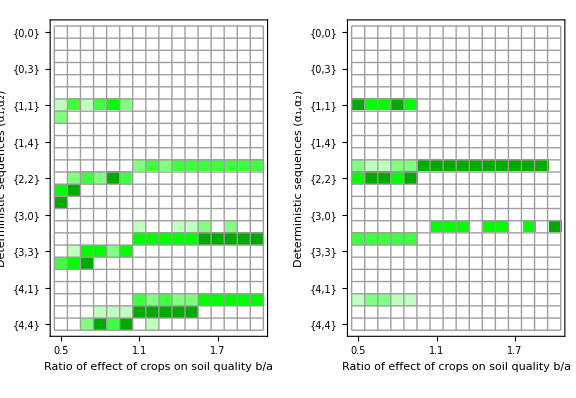

```mathematica
GraphicsRow[{plots⟦1⟧,plots⟦9⟧},ImageSize->Large]
```

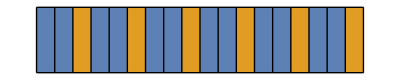

```mathematica
{covercol,cashcol}=ColorData[97,"ColorList"]⟦{1,2}⟧;
ArrayPlot[{{1,1,-1,1,1,-1,1,1,-1,1,1,-1,1,1,-1,1,1,-1}},ColorRules->{1->covercol,-1->cashcol},Mesh->True,MeshStyle->Black]
```